```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Mag[I_]:=Max[Abs[I]];
IsEmpty[x_Interval]:=Length[x]==0;
Wid[I_]:=Max[I]-Min[I];
Mid[I_]:=(Max[I]+Min[I])/2;
Attributes[Mag]={Listable};
Attributes[Wid]={Listable};
Attributes[Mid]={Listable};
Hull[pped[x_,m_,u_]]:=x+m.(Interval/@u);
IntervalVectorMemberQ[iv1_,iv2_]:=And@@((Min/@iv1≤Min/@iv2))&&And@@((Max/@iv2≤Max/@iv1));
IntervalVectorStrictMemberQ[iv1_,iv2_]:=And@@((Min/@iv1<Min/@iv2))&&And@@((Max/@iv2<Max/@iv1));
IntervalVectorIntersection[iv1_,iv2_]:=Map[Apply[IntervalIntersection,#]&,Transpose[{iv1,iv2}]];

enclVolume[ix_, iy_, pped[x_, m_, u_]] := (*Abs[Det[Take[m,{ix,iy},{ix,iy}]]] *)Times@@Wid[Interval/@Take[u,{ix,iy}]];
enclVolume[ix_, iy_, box[v_]] := -1;pipeVolume[ix_,iy_,volSet_,{t_,encl_}]:=Module[{vol},
vol=enclVolume[ix,iy,encl];
If[vol>0,Append[volSet,vol],volSet]
];

(*enclVolume[pped[x_, m_, u_]]:= Det[m]Times@@Wid[Interval/@u];*)
enclVolume[pped[x_, m_, u_]]:=Max[Wid[Hull[pped[x, m, u]]]];
enclVolume[box[v_]] := -1;
pipeVolume[volSet_,{t_,encl_}]:=Module[{vol},
vol=enclVolume[encl];
If[vol>0.,Append[volSet,vol],volSet]
];
```

```mathematica
plot[data_,plotRange_]:=Module[{plotData},
plotData=Fold[pipeVolume[1,2,#1,#2]&,{},data];
ListLogPlot[plotData[[1;;-2]],Joined->True,PlotRange->plotRange,PlotStyle->Directive[Black,Thickness[0.01]],AxesStyle->Directive[20,Thick],AspectRatio->4/5]
];
plot[data_]:=plot[data,Automatic];

plotCompare[dataPped_,dataBox_,n_]:=Module[{dp,db},
dp=Fold[pipeVolume[1,2,#1,#2]&,{},dataPped];
db=Fold[pipeVolume[1,2,#1,#2]&,{},dataBox];
Show[{ListLogPlot[db[[1;;-2]],Joined->True,PlotRange->{{1,n},{dp[[1]]/20,db[[-1]]}},PlotStyle->Directive[Black,Thickness[0.005],Dashed],AxesStyle->Directive[20,Thick]],ListLogPlot[dp[[1;;-2]],Joined->True,PlotRange->All,PlotStyle->Directive[Black,Thickness[0.01]],Axes->False]},AspectRatio->4/5]
];

plot1[data_,plotRange_]:=Module[{plotData},
plotData=Fold[pipeVolume[#1,#2]&,{},data];
ListLogPlot[plotData[[1;;-2]],Joined->True,PlotRange->plotRange,PlotStyle->Directive[Black,Thickness[0.01]],AxesStyle->Directive[20,Thick]]
];
plot1[data_]:=plot1[data,Automatic];

plotCompare1[dataPped_,dataBox_,n_,plotRange_]:=Module[{dp,db},
dp=Fold[pipeVolume[#1,#2]&,{},dataPped];
db=Fold[pipeVolume[#1,#2]&,{},dataBox];
Show[{ListLogPlot[db[[1;;-2]],Joined->True,PlotRange->plotRange,PlotStyle->Directive[Black,Thickness[0.01]],AxesStyle->Directive[20,Thick]],ListLogPlot[dp[[1;;-2]],Joined->True,PlotRange->plotRange,PlotStyle->Directive[Black,Thickness[0.005],Dashed],Axes->False]}]
];
```

```mathematica
list = <<"../src_ocaml/pped.dat";
(*list = <<"arc-e5c1o0.dat";*)
(*b=list[[1]][[2]]
enclVolume[1,2,b]*)
volSet=Fold[pipeVolume[1,1,#1,#2]&,{}, list];
m[ww_]:=Module[{a,b,c,w},NonlinearModelFit[Partition[volSet[[3;;-12]],2,1],a w^2+b w+c,{a,b,c},w][ww]];
m[10]
ListLogPlot[volSet[[1;;-2]](*,PlotRange->{10^-5,10^-3}*)]
```

7.13741×10^9

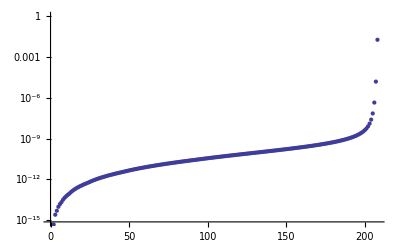
```mathematica
g9=-Graphics-
```

-Graphics-

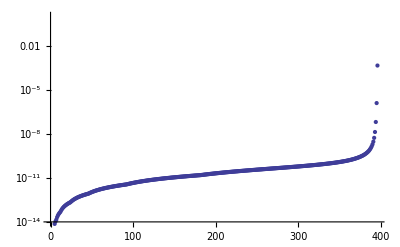
```mathematica
g10=-Graphics-
```

-Graphics-

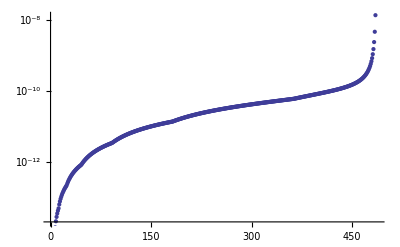
```mathematica
g11=-Graphics-
```

-Graphics-

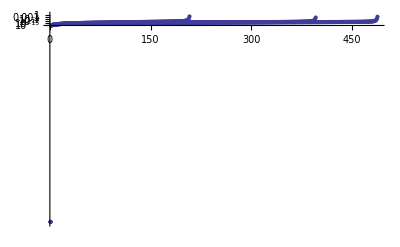

```mathematica
g=Show[{g9,g10,g11},PlotRange->Automatic]
```

```mathematica
Export["BehaviorXP.png",g]
```

BehaviorXP.png

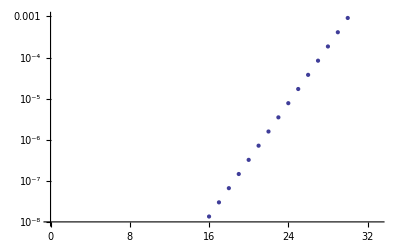

```mathematica
list = <<"../src_ocaml/pped.dat";
volSet=Fold[pipeVolume[2,2,#1,#2]&,{}, list];
ListLogPlot[volSet[[1;;-2]],PlotRange->{10^-8,10^-3}]
```

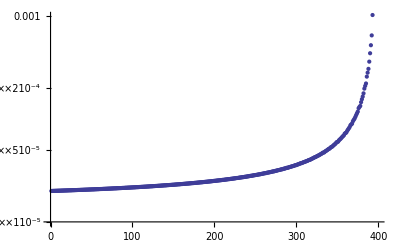

```mathematica
list = <<"../src_ocaml/pped1.dat";
(*b=list[[1]][[2]]
enclVolume[1,3,b]*)
volSet=Fold[pipeVolume[1,1,#1,#2]&,{}, list];
ListLogPlot[volSet[[1;;-2]],PlotRange->{10^-5,10^-3}]
```

```mathematica
Export["p.eps",pc]
```

p.eps

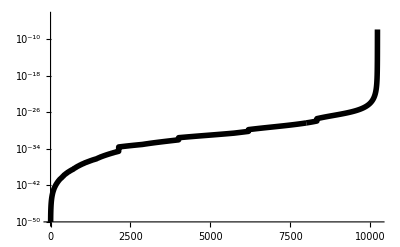

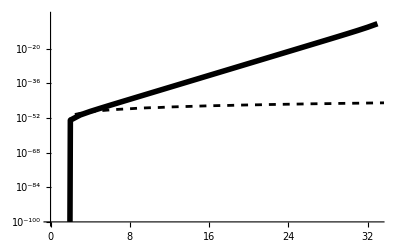

```mathematica
pp=plot1[<<"bb-parabola-2d.dat",{10^-50,10^-5}]
pc=plotCompare1[<<"bb-parabola-2d.dat",<<"bb-parabola-2d-box.dat",50,{10^-100,10^-5}]
```

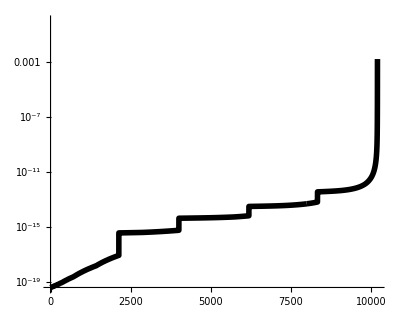

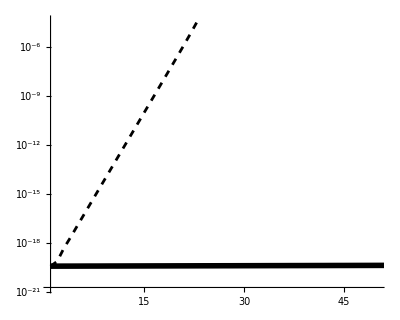

```mathematica
pp=plot[<<"bb-parabola-2d_.dat"]
pc=plotCompare[<<"bb-parabola-2d_.dat",<<"bb-parabola-2d-box_.dat",50]
```

```mathematica
list = <<../src_ocaml/pped.dat;
pp=list[[-2]][[2]]
enclVolume[pp]
volSet=Fold[pipeVolume[#1,#2]&,{}, list];
ListLogPlot[volSet[[1;;-2]],PlotRange->All]
```

pped[{-0.999992,0.,1.0000041560992781,1.414213562373092,0.,0.707101},{{0.640917,0.,0.313939,-0.606084,0.,-0.296877},{0.,-0.634009,0.,0.,6.5264193763682661,0.},{-0.313939,0.,0.640918,0.296878,0.,-0.606084},{0.294177,0.,0.144096,0.980157,0.,0.48011},{0.,0.911613,0.,0.,-10.9613157885140709,0.},{-0.144096,0.,0.294177,-0.48011,0.,0.980158}},{{-9.90757×10^-6,9.90757×10^-6},{0.,0.},{-4.67611×10^-7,4.67611×10^-7},{-1.26025×10^-7,1.26025×10^-7},{0.,0.},{-1.37891×10^-7,1.37891×10^-7}}]

{0.0000198151,4.45015×10^-308,9.35222×10^-7,2.5205×10^-7,4.45015×10^-308,2.75781×10^-7}

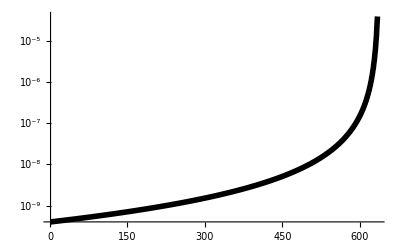

```mathematica
plot[<<disk-5.dat,Full]
```

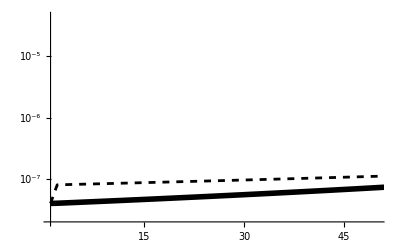

```mathematica
plotCompare[<<"../src_ocaml/pped.dat",<<"../src_ocaml/pped1.dat",50]
```

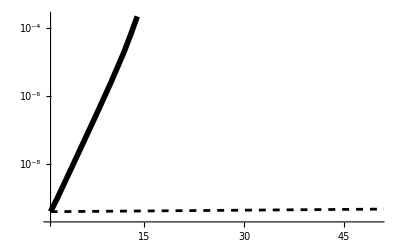

```mathematica
plotCompare[<<disk-5.dat,<<disk-5_box.dat,50]
```

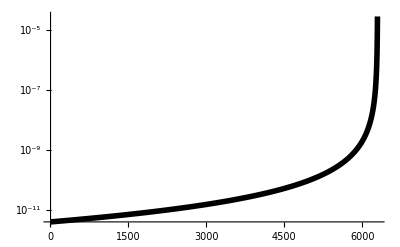

```mathematica
plot[<<disk-6.dat,Full]
```

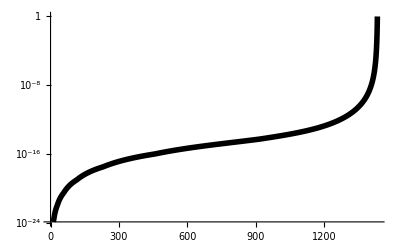

```mathematica
plot[<<bb-simple.dat]
```

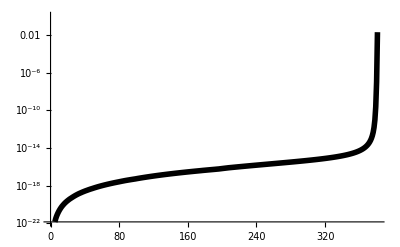

```mathematica
plot[<<bb-airfriction.dat]
```

```mathematica
plot["<<bb-parabola-2d.dat"]
```

Fold::normal: Fold[pipeVolume[1, 2, #1, #2] &, {}, "<<bb-parabola-2d.dat"]で3の位置に原子的ではない式が想定されます．

ListLogPlot::lpn: Fold[pipeVolume[1, 2, #1, #2] &, {}]は数値のリストあるいは数値の対のリストではありません．

ListLogPlot[Fold[pipeVolume[1,2,#1,#2]&,{}],Joined→True,PlotRange→Automatic,PlotStyle→Directive[GrayLevel[0],Thickness[0.01]],AxesStyle→Directive[20,Thickness[Large]]]